#### Computing the surface contribution to the energy of a round particle from LJ

```mathematica
hexLatticeVectors = {{1,0},{1/2,Sqrt[3]/2}}
```

{{1,0},{1/2,(√3)/2}}

```mathematica
latticePoints = #.hexLatticeVectors&/@N@Tuples[N@Range[-60,60],2];
```

```mathematica
particle = Select[Norm[#]<50&][latticePoints];
```

#### We can make round particles up to about size 50 with the part of the lattice we chose.

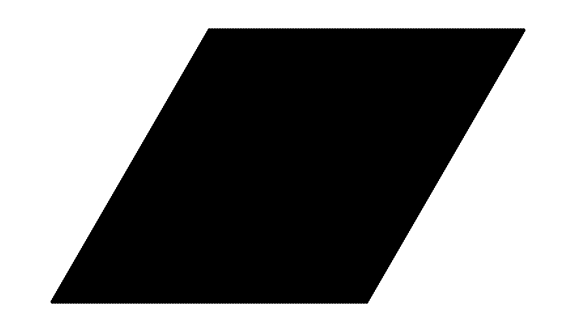

```mathematica
Graphics[{Point/@latticePoints,Circle[#,1/2]&/@particle},ImageSize->Large]
```

```mathematica
roundParticle[radius_,latticePoints_]:= Select[Norm[#]<radius&][latticePoints]
```

#### Using DistanceMatrix, find the energy of each particle.

An identity matrix is added to the DistanceMatrix. This is because the diagonal of the DistanceMatrix is full of zeroes (these terms represent the distance of an atom to itself). This is done so that  there are no divisions by zero.  Those additional terms are subtracted at the end

```mathematica
lennardJonesTotalEnergyPerParticle[positions_]:=
Block[{augmentedDistanceMatrix= DistanceMatrix[positions, DistanceFunction->EuclideanDistance]+ IdentityMatrix[Length[positions]],
pairEnergies,
energiesPerParticle},
pairEnergies = 1/augmentedDistanceMatrix^12- 2/augmentedDistanceMatrix^6;
energiesPerParticle =( Total[pairEnergies]/2 ) + 1/2
]
```

#### For a particle of size 20, here are the range of energies:

```mathematica
{eMin,eMax}=MinMax[lennardJonesTotalEnergyPerParticle[roundParticle[20,latticePoints]]]
```

{-2.87096,-1.18183}

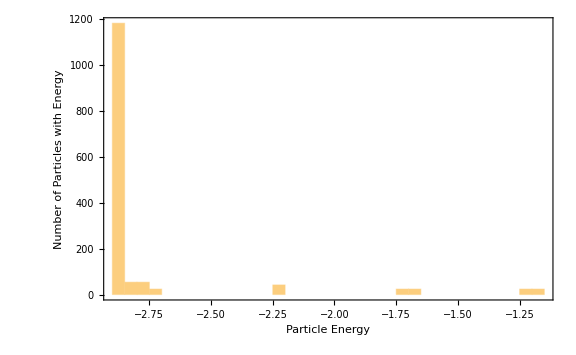

```mathematica
Histogram[lennardJonesTotalEnergyPerParticle[roundParticle[20,latticePoints]],{.05},Frame->True,FrameLabel->{"Particle Energy","Number of Particles with Energy"},
ImageSize->Large]
```

#### Function to color particles according to their energy, Give more contrast to the lower energy part of the distribution

```mathematica
energyColor[energy_,{eMin_, eMax_}]:= ColorData["DarkRainbow"][
(Rescale[Clip[energy,{eMin,eMax}],{eMin,eMax},{0,1}])^(.25)]
```

```mathematica
energyColor[#,{eMin,eMax}]&/@Range[eMin,eMax,(eMax-eMin)/24]
```

{RGBColor[0.178927, 0.305394, 0.933501],RGBColor[0.9561442317663132, 0.966813020375322, 0.9591205555900935],RGBColor[0.9891538832635385, 0.9897828662440565, 0.8294117533809076],RGBColor[0.9949061605644446, 0.9915131174505429, 0.6869451968519318],RGBColor[0.9934275253595953, 0.988350466260322, 0.5260048798828034],RGBColor[0.9885858780601058, 0.9731596279127674, 0.41015872094992],RGBColor[0.9747708185853227, 0.9265581883741022, 0.35648982364546056],RGBColor[0.9625889063200481, 0.8854657378543099, 0.30916539485596994],RGBColor[0.9498566916055505, 0.8389055220226553, 0.27851172093234605],RGBColor[0.9357597049919705, 0.7830156676421258, 0.2671689546042552],RGBColor[0.9227929278097541, 0.731606717036986, 0.2567355813140645],RGBColor[0.9107651626357941, 0.6839206361373811, 0.2470577591271617],RGBColor[0.9000683335229316, 0.6391154668088647, 0.23832690675329074],RGBColor[0.8907226283245816, 0.5966788022480624, 0.23052862125159043],RGBColor[0.8819015323004464, 0.5566242654217841, 0.22316808250420256],RGBColor[0.8735410852391788, 0.5186614279485887, 0.21619192054297073],RGBColor[0.8655887878870763, 0.4825519029789248, 0.20955632870373095],RGBColor[0.858042730703709, 0.4471474394412896, 0.20321509051274708],RGBColor[0.8515330251071737, 0.39711098965513725, 0.19698138908184393],RGBColor[0.8452891684313101, 0.3491179711690083, 0.1910022648776095],RGBColor[0.8392871292738966, 0.30298366809479926, 0.1852547054021367],RGBColor[0.8335061230212952, 0.25854832078421197, 0.1797188072859329],RGBColor[0.8279280415562922, 0.21567274231331443, 0.174377230175504],RGBColor[0.8225370041968378, 0.17423486680091466, 0.16921476671178476],RGBColor[0.817319, 0.134127, 0.164218]}

```mathematica
particleGraphic[positions_]:= MapThread[{energyColor[#1,{eMin,eMax}],Disk[#2,1/2]}&,{lennardJonesTotalEnergyPerParticle[positions],positions}]
```

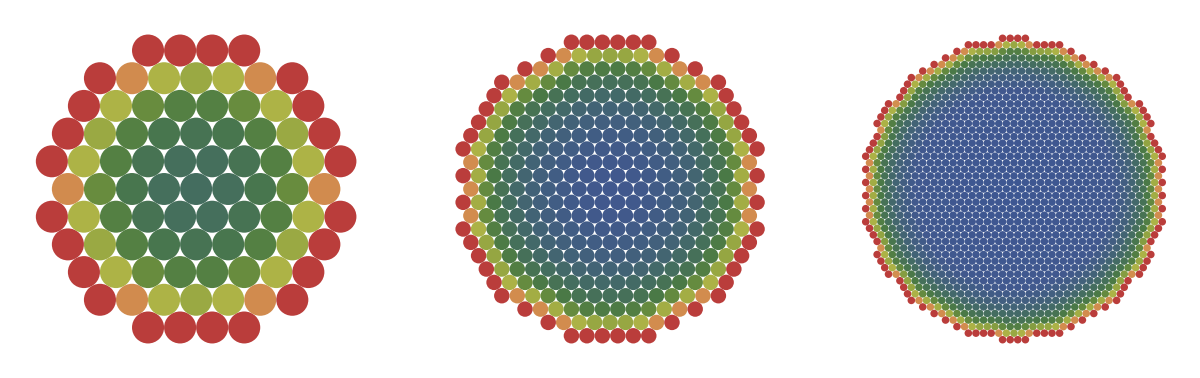

```mathematica
GraphicsRow[
Graphics[particleGraphic[roundParticle[#,latticePoints]]]&/@{5,10,20}]
```

#### Compute excess energy due to surface

We will compute the Lennard-Jones total energy of  particles for a number of different radii.  Then we will try to extract the excess energy due to a surface.

```mathematica
particles = <| # -> roundParticle[#,N[latticePoints]]&/@Range[5,50] |>;
```

For example:

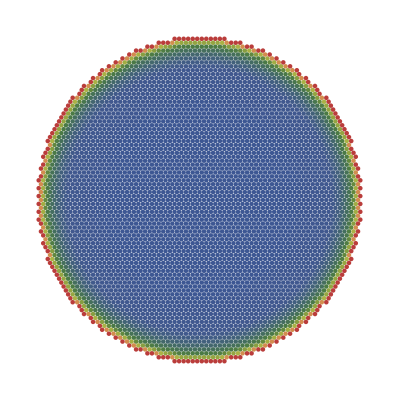

```mathematica
Graphics[
particleGraphic[particles[36]]
]
```

```mathematica
totalLennardJonesTotalEnergy[positions_]:=Total[lennardJonesTotalEnergyPerParticle[positions]]
```

#### Here is an example for a particle of radius 5 diameters:

```mathematica
totalLennardJonesTotalEnergy[roundParticle[10,latticePoints]]
```

-(16175475411099868043464718841789921583923300679954248413212863249052544434178694274972313269628595271429941103329221829422025856079934030360994474113536115246105881980061339720134032296933860055195764838823949399717797331382209143180428604381111162057832250491460973420104692537415360484664252686650297713668716696467859753791995403431376267323390420096223191020466985068017409940744610383481553741221030163245046168225003965145289817267558504082499433778868869441151107904694906907858871431771631980458875170241703242968718626657042142592442776593/17021464402043897947617784084686310355410142710290879914001307707118520983362276375806693631712138173379491552951119026625311187040442856560117149849726439339300924653530716567532008915663757423178254402304400243009996684054979247564553025628040560750933106689959854707873806674322782119421849898673945193071919662055569307300787380068908388102122188240226693347422078545597847271706249728465150932500873034241591666605954070320514380893675924883436536707411549843586088508920363695699169863368179916992423208287092018678800333144064000000000000)

#### This is a case were exact computation is going to take a long time clearing fractions and what-not. Numerical calculations are going to be faster. Nevertheless, the next computation will take about 20 seconds:

```mathematica
energyData=Block[{totalEnergy =totalLennardJonesTotalEnergy[#]},
<|"Total Energy"-> totalEnergy, "Average Energy"-> totalEnergy/Length[#]|>]&/@particles
```

<|5→<|Total Energy→-202.796,Average Energy→-2.38583|>,6→<|Total Energy→-298.484,Average Energy→-2.46681|>,7→<|Total Energy→-422.4,Average Energy→-2.49941|>,8→<|Total Energy→-603.887,Average Energy→-2.56973|>,9→<|Total Energy→-768.479,Average Energy→-2.60501|>,10→<|Total Energy→-950.299,Average Energy→-2.63241|>,11→<|Total Energy→-1149.34,Average Energy→-2.65438|>,12→<|Total Energy→-1365.62,Average Energy→-2.67244|>,13→<|Total Energy→-1599.11,Average Energy→-2.68759|>,14→<|Total Energy→-1895.07,Average Energy→-2.6957|>,15→<|Total Energy→-2214.68,Average Energy→-2.71074|>,16→<|Total Energy→-2517.08,Average Energy→-2.72117|>,17→<|Total Energy→-2836.71,Average Energy→-2.73023|>,18→<|Total Energy→-3173.56,Average Energy→-2.73819|>,19→<|Total Energy→-3527.64,Average Energy→-2.74524|>,20→<|Total Energy→-3995.77,Average Energy→-2.75001|>,21→<|Total Energy→-4401.52,Average Energy→-2.75612|>,22→<|Total Energy→-4858.95,Average Energy→-2.76234|>,23→<|Total Energy→-5299.16,Average Energy→-2.76718|>,24→<|Total Energy→-5756.59,Average Energy→-2.77159|>,25→<|Total Energy→-6265.69,Average Energy→-2.77611|>,26→<|Total Energy→-6768.59,Average Energy→-2.77743|>,27→<|Total Energy→-7363.6,Average Energy→-2.78187|>,28→<|Total Energy→-7907.16,Average Energy→-2.78519|>,29→<|Total Energy→-8502.4,Average Energy→-2.78859|>,30→<|Total Energy→-9080.41,Average Energy→-2.7914|>,31→<|Total Energy→-9675.65,Average Energy→-2.79401|>,32→<|Total Energy→-10322.6,Average Energy→-2.79668|>,33→<|Total Energy→-11031.9,Average Energy→-2.79785|>,34→<|Total Energy→-11730.5,Average Energy→-2.80032|>,35→<|Total Energy→-12411.9,Average Energy→-2.80242|>,36→<|Total Energy→-13144.9,Average Energy→-2.80455|>,37→<|Total Energy→-13860.8,Average Energy→-2.80639|>,38→<|Total Energy→-14662.6,Average Energy→-2.80839|>,39→<|Total Energy→-15475.4,Average Energy→-2.80911|>,40→<|Total Energy→-16329.,Average Energy→-2.81098|>,41→<|Total Energy→-17165.4,Average Energy→-2.81262|>,42→<|Total Energy→-17984.6,Average Energy→-2.81405|>,43→<|Total Energy→-18855.4,Average Energy→-2.8155|>,44→<|Total Energy→-19743.5,Average Energy→-2.81688|>,45→<|Total Energy→-20648.8,Average Energy→-2.81818|>,46→<|Total Energy→-21633.8,Average Energy→-2.81873|>,47→<|Total Energy→-22590.8,Average Energy→-2.81997|>,48→<|Total Energy→-23565.,Average Energy→-2.82114|>,49→<|Total Energy→-24522.,Average Energy→-2.82218|>,50→<|Total Energy→-25565.1,Average Energy→-2.82331|>|>

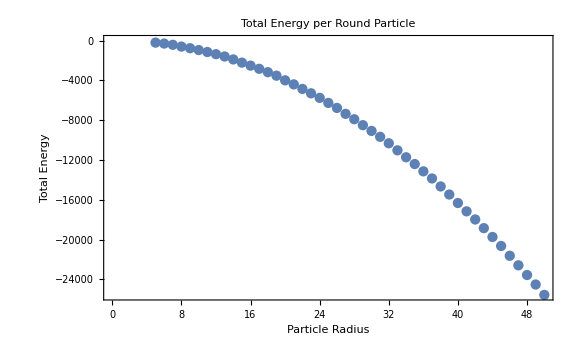

```mathematica
totalEnergyPlot =
ListPlot[energyData[[All,"Total Energy"]],Frame->True,FrameLabel->{"Particle Radius","Total Energy"},ImageSize->Large,
PlotLabel-> "Total Energy per Round Particle",BaseStyle->{FontSize->16}]
```

Remember, the bonding energy (in normalized units) is -1.  Without a surface, we would expect the total energy to decrease linear with the number of particles

#### Average Energy per particle:

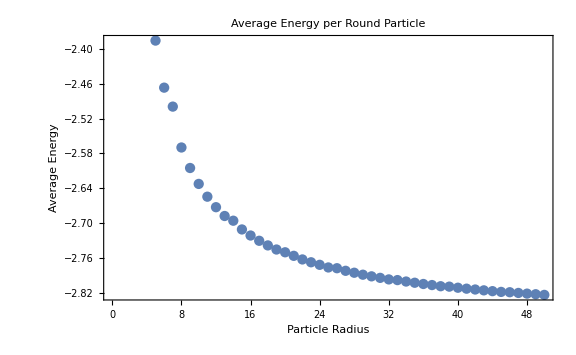

```mathematica
ListPlot[energyData[[All,"Average Energy"]],Frame->True,FrameLabel->{"Particle Radius","Average Energy"},ImageSize->Large,
PlotLabel-> "Average Energy per Round Particle",BaseStyle->{FontSize->16}]
```

Let’s extrapolate to find what the average energy is when the particle size goes to infinity (when the particle size becomes very large, the fraction of particles on the surface becomes small and its effect on the average energy should vanish.

```mathematica
averageEnergyModel = constantValue + sizeDependence /radius^power
```

constantValue+radius^-power sizeDependence

```mathematica
averageEnergyFitData =KeyValueMap[List,energyData[[All,"Average Energy"]]]
```

{{5,-2.38583},{6,-2.46681},{7,-2.49941},{8,-2.56973},{9,-2.60501},{10,-2.63241},{11,-2.65438},{12,-2.67244},{13,-2.68759},{14,-2.6957},{15,-2.71074},{16,-2.72117},{17,-2.73023},{18,-2.73819},{19,-2.74524},{20,-2.75001},{21,-2.75612},{22,-2.76234},{23,-2.76718},{24,-2.77159},{25,-2.77611},{26,-2.77743},{27,-2.78187},{28,-2.78519},{29,-2.78859},{30,-2.7914},{31,-2.79401},{32,-2.79668},{33,-2.79785},{34,-2.80032},{35,-2.80242},{36,-2.80455},{37,-2.80639},{38,-2.80839},{39,-2.80911},{40,-2.81098},{41,-2.81262},{42,-2.81405},{43,-2.8155},{44,-2.81688},{45,-2.81818},{46,-2.81873},{47,-2.81997},{48,-2.82114},{49,-2.82218},{50,-2.82331}}

```mathematica
averageEnergyFit=FindFit[averageEnergyFitData,averageEnergyModel,{constantValue,sizeDependence,power},radius]
```

{constantValue→-2.86986,sizeDependence→2.53214,power→1.02108}

We see that the excess energy per atom goes like:



This is related to the Gibbs-Thomson effect which relates the chemical potential or vapor pressure of a small particle to its size.  Smaller solid particles will also melt before large particles.

#### Suppose that the excess energy goes as the particle’s area over the particle’s perimeter

```mathematica
totalEnergymodel = bulkEnergy (Pi radius^2) + γ (2 Pi radius)
```

bulkEnergy π radius^2+2 π radius γ

```mathematica
totalEnergyFitData =KeyValueMap[List,energyData[[All,"Total Energy"]]]
```

{{5,-202.796},{6,-298.484},{7,-422.4},{8,-603.887},{9,-768.479},{10,-950.299},{11,-1149.34},{12,-1365.62},{13,-1599.11},{14,-1895.07},{15,-2214.68},{16,-2517.08},{17,-2836.71},{18,-3173.56},{19,-3527.64},{20,-3995.77},{21,-4401.52},{22,-4858.95},{23,-5299.16},{24,-5756.59},{25,-6265.69},{26,-6768.59},{27,-7363.6},{28,-7907.16},{29,-8502.4},{30,-9080.41},{31,-9675.65},{32,-10322.6},{33,-11031.9},{34,-11730.5},{35,-12411.9},{36,-13144.9},{37,-13860.8},{38,-14662.6},{39,-15475.4},{40,-16329.},{41,-17165.4},{42,-17984.6},{43,-18855.4},{44,-19743.5},{45,-20648.8},{46,-21633.8},{47,-22590.8},{48,-23565.},{49,-24522.},{50,-25565.1}}

```mathematica
totalEnergyFit = FindFit[totalEnergyFitData,totalEnergymodel,{bulkEnergy,γ},radius]
```

{bulkEnergy→-3.32211,γ→1.6384}

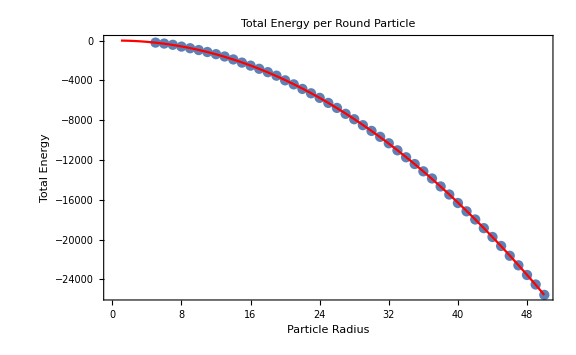

```mathematica
Show[totalEnergyPlot,Plot[totalEnergymodel/.totalEnergyFit,{radius,1,50},PlotStyle->Red]]
```

We can conclude that the surface tension of our LJ particles is  about   and the energy per unit area is about .

You might notice there might be a discrepancy between our two fits:

```mathematica
totalEnergyFit
```

{bulkEnergy→-3.32211,γ→1.6384}

```mathematica
averageEnergyFit
```

{constantValue→-2.86986,sizeDependence→2.53214,power→1.02108}

Shouldn’t the size independent terms be the same?

```mathematica
(constantValue/.averageEnergyFit)/(bulkEnergy/.totalEnergyFit)
```

0.863868

The discrepancy is resolved by noting that the bulk energy fit is the energy per unit area; the average energy fit is energy per atom.  Each atom in our hexagonal lattice takes up  normalized units of area which is roughly the same ratio as our size independent terms.

```mathematica
Sqrt[3]/2.0
```

0.866025

#### We conclude—tentatively—that the surface tension for LJ is about 1.64 eMin/rMin^2.

### Strain Relaxation

All of our work above was performed as if our particle’s lattice constant had a fixed value of 1 (i.e., 1 rMin). 
We will  find that that this value doesn’t give the lowest bulk energy and the particle would rather shrink a bit.

These would be the positions of a particle of radius 5 with a different lattice constant:

```mathematica
(newLatticeConstant particles[5])[[1;;3]]
```

{{-4.5 newLatticeConstant,0.866025 newLatticeConstant},{-4. newLatticeConstant,1.73205 newLatticeConstant},{-3.5 newLatticeConstant,2.59808 newLatticeConstant}}

For example

```mathematica
energyR3 =Apart@Simplify[
totalLennardJonesTotalEnergy[ newLatticeConstant roundParticle[3,latticePoints]],
Assumptions->newLatticeConstant>0]
```

1018825364171071593858613997979162929100750383/(14131596803662749596338252689408000000000000 newLatticeConstant^12)-163566117757392461769629/(1085188033002528000000 newLatticeConstant^6)

Minimizing this for newLatticeConstant will result in six solutions but—if we look at the 6^thpower of the minimizing lattice constant—they are all the same

```mathematica
SolveValues[D[energyR3,newLatticeConstant]== 0, newLatticeConstant]^6
```

{1018825364171071593858613997979162929100750383/1064999961570027551655012490758663732672000000,1018825364171071593858613997979162929100750383/1064999961570027551655012490758663732672000000,1018825364171071593858613997979162929100750383/1064999961570027551655012490758663732672000000,1018825364171071593858613997979162929100750383/1064999961570027551655012490758663732672000000,1018825364171071593858613997979162929100750383/1064999961570027551655012490758663732672000000,1018825364171071593858613997979162929100750383/1064999961570027551655012490758663732672000000}

#### Or, because we can write the total energy in this form:

```mathematica
Clear[twelfthPowerCoefficient,sixthPowerCoefficient]
```

```mathematica
symbolicTotalEnergy = twelfthPowerCoefficient/newLatticeConstant^12  -2 sixthPowerCoefficient/newLatticeConstant^6
```

-(2 sixthPowerCoefficient)/newLatticeConstant^6+twelfthPowerCoefficient/newLatticeConstant^12

```mathematica
First[
SolveValues[D[symbolicTotalEnergy,newLatticeConstant]==0,newLatticeConstant]^6
]
```

twelfthPowerCoefficient/sixthPowerCoefficient

We can just modify our total energy function to return the minimizing lattice constant:

```mathematica
minimizingLatticeConstant[unitLatticeConstantPositions_]:=
Block[{augmentedDistanceMatrix= DistanceMatrix[unitLatticeConstantPositions, DistanceFunction->EuclideanDistance], identity=IdentityMatrix[Length[unitLatticeConstantPositions]],
twelfthPowerCoefficient,sixthPowerCoefficient
},
augmentedDistanceMatrix = augmentedDistanceMatrix+ identity;
twelfthPowerCoefficient=  Total[Total[1/augmentedDistanceMatrix^12 -identity]];
sixthPowerCoefficient=  Total[Total[1/augmentedDistanceMatrix^6 -identity]];
(twelfthPowerCoefficient/sixthPowerCoefficient)^(1/6)

]
```

```mathematica
minimizingLatticeConstant[roundParticle[3,latticePoints]]
```

(1018825364171071593858613997979162929100750383/163566117757392461769629)^(1/6)/(60 √5187)

```mathematica
minimizingLatticeConstant[particles[5]]
```

0.991639

Collecting data to fit:

```mathematica
latticeConstantData=
minimizingLatticeConstant/@particles
```

<|5→0.991639,6→0.991403,7→0.991121,8→0.990995,9→0.990912,10→0.990846,11→0.990792,12→0.990747,13→0.990708,14→0.990652,15→0.990617,16→0.990593,17→0.990572,18→0.990553,19→0.990536,20→0.990509,21→0.990496,22→0.990481,23→0.99047,24→0.99046,25→0.990449,26→0.990435,27→0.990427,28→0.990419,29→0.990411,30→0.990405,31→0.990399,32→0.990393,33→0.990384,34→0.990379,35→0.990374,36→0.990369,37→0.990365,38→0.990361,39→0.990355,40→0.99035,41→0.990347,42→0.990344,43→0.99034,44→0.990337,45→0.990334,46→0.99033,47→0.990327,48→0.990324,49→0.990322,50→0.99032|>

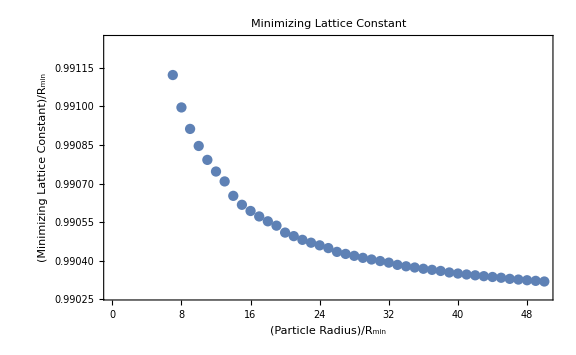

```mathematica
latticeConstantPlot =ListPlot[latticeConstantData,Frame->True,FrameLabel->{"(Particle Radius)/R_min","(Minimizing Lattice Constant)/R_min"},ImageSize->Large,
PlotLabel-> "Minimizing Lattice Constant",BaseStyle->{FontSize->16}]
```

```mathematica
latticeConstantModel = rLimit + powerCoefficient/radius^power;
```

```mathematica
latticeConstantFit =With[{dataPairs=KeyValueMap[List,latticeConstantData]},FindFit[dataPairs,latticeConstantModel,{rLimit,powerCoefficient,power},radius]
]
```

{rLimit→0.990231,powerCoefficient→0.00918785,power→1.17073}

The fit is a bit wonky because the smaller radii particles are not very circular, in fact the power should go to 1;  so we will remove the data for the smaller particles:

```mathematica
latticeConstantFit =With[{dataPairs=KeyValueMap[List,latticeConstantData]},FindFit[dataPairs[[10;;-1]],latticeConstantModel,{rLimit,powerCoefficient,power},radius]
]
```

{rLimit→0.990193,powerCoefficient→0.00671774,power→1.01682}

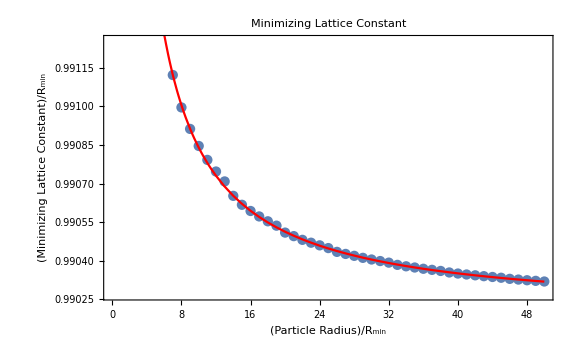

```mathematica
Show[latticeConstantPlot,Plot[latticeConstantModel/.latticeConstantFit,{radius,1,50},PlotStyle->Red]]
```

We can conclude that the limiting lattice constant is about 1% smaller than rMin.  This arises from the long range attraction from the 1/r^6 term.  The reduced lattice constant for smaller particles is a known phenomenon and has been  observed by x-ray scattering .

We now need to re-evaluate the surface energy for the relaxed lattice.

```mathematica
latticeConstantModel/.{rLimit->0.9901932620480345,powerCoefficient->0.006717735195661647,power->1.0168160973765517}
```

0.990193+0.00671774/radius^1.01682

```mathematica
relaxedParticles = <| # -> roundParticle[#,N[latticePoints](0.9901932620480345+0.006717735195661647/#^1.0168160973765517)]&/@Range[5,50] |>;
```

<|5→{{-4.9575,0.},{-4.46175,0.858665},87,{4.46175,-0.858665},{4.9575,0.}},44,50→{{-45.5547,20.5834},9270}|>
 |  |  |  |

```mathematica
relaxedEnergyData=Block[{totalEnergy =totalLennardJonesTotalEnergy[#]},
<|"Total Energy"-> totalEnergy, "Average Energy"-> totalEnergy/Length[#]|>]&/@relaxedParticles;
KeySort@RandomSample[relaxedEnergyData,5]
```

<|5→<|Total Energy→-265.614,Average Energy→-2.91883|>,8→<|Total Energy→-743.222,Average Energy→-3.08391|>,9→<|Total Energy→-938.406,Average Energy→-3.11763|>,18→<|Total Energy→-3865.48,Average Energy→-3.25103|>,36→<|Total Energy→-15841.6,Average Energy→-3.31622|>|>

Our previous fit was:

```mathematica
totalEnergyFit = FindFit[totalEnergyFitData,totalEnergymodel,{bulkEnergy,γ},radius]
```

{bulkEnergy→-3.32211,γ→1.6384}

```mathematica
relaxedTotalEnergyFitData =KeyValueMap[List,relaxedEnergyData[[All,"Total Energy"]]];
```

```mathematica
totalEnergyFit = FindFit[relaxedTotalEnergyFitData,totalEnergymodel,{bulkEnergy,γ},radius]
```

{bulkEnergy→-3.97194,γ→1.24918}

A better value for the surface tension reduced by about 25%.

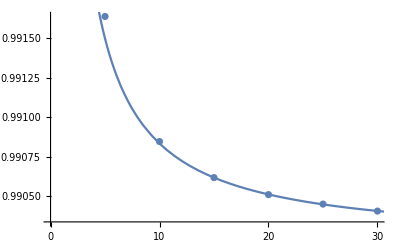

```mathematica
Show[ListPlot[latticeConstantData],Plot[model/.fit,{r,0,35}]]
```

It is also worth asking if our assumption of uniform strain (i.e., a fixed but smaller lattice constant) is ok.
Why not, for example, allow each of the atoms find their own minimizing position?

In fact, this would be a better approach and would give an even smaller values of surface and bulk energy.  However, minimizing a function over many variables is numerically slow.
We will come back to this topic later, but first we are going to investigate another phenomenon.

#### The orientation dependence of surface energy density.

# Stopped here for the time being.

```mathematica
N[%]
```

{-203.389,{a→-0.991639}}

```mathematica
Simplify[totalLennardJonesTotalEnergy[p],Assumptions->a>0]
```

$Aborted

#### Particle Size and Lattice Constant effect

#### Surface Relaxation The positions we specified were as if they were on a perfect lattice, in a real system they would all relax to an equilbrium with lower internal energy.

Trying to find the equilibrium positions with FindMinimum. I thought I had done this once, but can’t figure it out now

```mathematica
p =N@roundParticle[5,latticePoints];
```

```mathematica
Length[p]
```

85

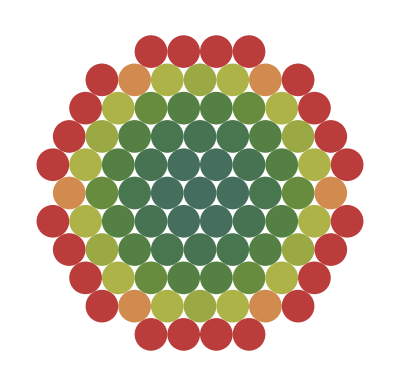

```mathematica
Graphics[particleGraphic[p]]
```

```mathematica
pairs={x[#],y[#]}&/@Range[Length[p]];
vars = Flatten[pairs]
```

{x[1],y[1],x[2],y[2],x[3],y[3],x[4],y[4],x[5],y[5],x[6],y[6],x[7],y[7],x[8],y[8],x[9],y[9],x[10],y[10],x[11],y[11],x[12],y[12],x[13],y[13],x[14],y[14],x[15],y[15],x[16],y[16],x[17],y[17],x[18],y[18],x[19],y[19],x[20],y[20],x[21],y[21],x[22],y[22],x[23],y[23],x[24],y[24],x[25],y[25],x[26],y[26],x[27],y[27],x[28],y[28],x[29],y[29],x[30],y[30],x[31],y[31],x[32],y[32],x[33],y[33],x[34],y[34],x[35],y[35],x[36],y[36],x[37],y[37],x[38],y[38],x[39],y[39],x[40],y[40],x[41],y[41],x[42],y[42],x[43],y[43],x[44],y[44],x[45],y[45],x[46],y[46],x[47],y[47],x[48],y[48],x[49],y[49],x[50],y[50],x[51],y[51],x[52],y[52],x[53],y[53],x[54],y[54],x[55],y[55],x[56],y[56],x[57],y[57],x[58],y[58],x[59],y[59],x[60],y[60],x[61],y[61],x[62],y[62],x[63],y[63],x[64],y[64],x[65],y[65],x[66],y[66],x[67],y[67],x[68],y[68],x[69],y[69],x[70],y[70],x[71],y[71],x[72],y[72],x[73],y[73],x[74],y[74],x[75],y[75],x[76],y[76],x[77],y[77],x[78],y[78],x[79],y[79],x[80],y[80],x[81],y[81],x[82],y[82],x[83],y[83],x[84],y[84],x[85],y[85]}

```mathematica
totalLennardJonesTotalEnergy[p]
```

-202.796

```mathematica
totalLennardJonesTotalEnergyFlat[Flatten[p]]
```

-202.796

```mathematica
guess=Transpose[{vars,Flatten[p]}]
```

{{x[1],-4.5},{y[1],0.866025},{x[2],-4.},{y[2],1.73205},{x[3],-3.5},{y[3],2.59808},{x[4],-3.},{y[4],3.4641},{x[5],-4.5},{y[5],-0.866025},{x[6],-4.},{y[6],0.},{x[7],-3.5},{y[7],0.866025},{x[8],-3.},{y[8],1.73205},{x[9],-2.5},{y[9],2.59808},{x[10],-2.},{y[10],3.4641},{x[11],-1.5},{y[11],4.33013},{x[12],-4.},{y[12],-1.73205},{x[13],-3.5},{y[13],-0.866025},{x[14],-3.},{y[14],0.},{x[15],-2.5},{y[15],0.866025},{x[16],-2.},{y[16],1.73205},{x[17],-1.5},{y[17],2.59808},{x[18],-1.},{y[18],3.4641},{x[19],-0.5},{y[19],4.33013},{x[20],-3.5},{y[20],-2.59808},{x[21],-3.},{y[21],-1.73205},{x[22],-2.5},{y[22],-0.866025},{x[23],-2.},{y[23],0.},{x[24],-1.5},{y[24],0.866025},{x[25],-1.},{y[25],1.73205},{x[26],-0.5},{y[26],2.59808},{x[27],0.},{y[27],3.4641},{x[28],0.5},{y[28],4.33013},{x[29],-3.},{y[29],-3.4641},{x[30],-2.5},{y[30],-2.59808},{x[31],-2.},{y[31],-1.73205},{x[32],-1.5},{y[32],-0.866025},{x[33],-1.},{y[33],0.},{x[34],-0.5},{y[34],0.866025},{x[35],0.},{y[35],1.73205},{x[36],0.5},{y[36],2.59808},{x[37],1.},{y[37],3.4641},{x[38],1.5},{y[38],4.33013},{x[39],-2.},{y[39],-3.4641},{x[40],-1.5},{y[40],-2.59808},{x[41],-1.},{y[41],-1.73205},{x[42],-0.5},{y[42],-0.866025},{x[43],0.},{y[43],0.},{x[44],0.5},{y[44],0.866025},{x[45],1.},{y[45],1.73205},{x[46],1.5},{y[46],2.59808},{x[47],2.},{y[47],3.4641},{x[48],-1.5},{y[48],-4.33013},{x[49],-1.},{y[49],-3.4641},{x[50],-0.5},{y[50],-2.59808},{x[51],0.},{y[51],-1.73205},{x[52],0.5},{y[52],-0.866025},{x[53],1.},{y[53],0.},{x[54],1.5},{y[54],0.866025},{x[55],2.},{y[55],1.73205},{x[56],2.5},{y[56],2.59808},{x[57],3.},{y[57],3.4641},{x[58],-0.5},{y[58],-4.33013},{x[59],0.},{y[59],-3.4641},{x[60],0.5},{y[60],-2.59808},{x[61],1.},{y[61],-1.73205},{x[62],1.5},{y[62],-0.866025},{x[63],2.},{y[63],0.},{x[64],2.5},{y[64],0.866025},{x[65],3.},{y[65],1.73205},{x[66],3.5},{y[66],2.59808},{x[67],0.5},{y[67],-4.33013},{x[68],1.},{y[68],-3.4641},{x[69],1.5},{y[69],-2.59808},{x[70],2.},{y[70],-1.73205},{x[71],2.5},{y[71],-0.866025},{x[72],3.},{y[72],0.},{x[73],3.5},{y[73],0.866025},{x[74],4.},{y[74],1.73205},{x[75],1.5},{y[75],-4.33013},{x[76],2.},{y[76],-3.4641},{x[77],2.5},{y[77],-2.59808},{x[78],3.},{y[78],-1.73205},{x[79],3.5},{y[79],-0.866025},{x[80],4.},{y[80],0.},{x[81],4.5},{y[81],0.866025},{x[82],3.},{y[82],-3.4641},{x[83],3.5},{y[83],-2.59808},{x[84],4.},{y[84],-1.73205},{x[85],4.5},{y[85],-0.866025}}

```mathematica
totalLennardJonesTotalEnergy[p]
```

-202.796

```mathematica
totalLennardJonesTotalEnergy[p]
```

```mathematica
Reap[{min,sol}=FindMinimum[totalLennardJonesTotalEnergyFlat[vars],guess,PrecisionGoal->50, AccuracyGoal->40,MaxIterations->100,Method->"PrincipalAxis",
StepMonitor:>Sow[totalLennardJonesTotalEnergyFlat[vars]]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{-203.428,{x[1]→-4.46551,y[1]→0.852544,x[2]→-3.96655,y[2]→1.71687,x[3]→-3.46992,y[3]→2.57676,x[4]→-2.97054,y[4]→3.43733,x[5]→-4.46537,y[5]→-0.855568,x[6]→-3.9624,y[6]→-0.000984908,x[7]→-3.46763,y[7]→0.857504,x[8]→-2.97213,y[8]→1.71495,x[9]→-2.47611,y[9]→2.57165,x[10]→-1.97982,y[10]→3.42903,x[11]→-1.49133,y[11]→4.29152,x[12]→-3.96816,y[12]→-1.71757,x[13]→-3.46767,y[13]→-0.859223,x[14]→-2.9714,y[14]→-0.000957014,x[15]→-2.47652,y[15]→0.856663,x[16]→-1.98086,y[16]→1.7136,x[17]→-1.4849,y[17]→2.57069,x[18]→-0.98932,y[18]→3.42937,x[19]→-0.49608,y[19]→4.29166,x[20]→-3.47185,y[20]→-2.57819,x[21]→-2.97348,y[21]→-1.71708,x[22]→-2.47702,y[22]→-0.859095,x[23]→-1.98136,y[23]→-0.00141794,x[24]→-1.48602,y[24]→0.855899,x[25]→-0.990151,y[25]→1.71316,x[26]→-0.494761,y[26]→2.571,x[27]→0.000624145,y[27]→3.42965,x[28]→0.497441,y[28]→4.2915,x[29]→-2.97386,y[29]→-3.43992,x[30]→-2.47826,y[30]→-2.57424,x[31]→-1.98233,y[31]→-1.71657,x[32]→-1.48661,y[32]→-0.85914,x[33]→-0.991074,y[33]→-0.00175741,x[34]→-0.495601,y[34]→0.855515,x[35]→-0.0000429739,y[35]→1.71296,x[36]→0.495219,y[36]→2.57063,x[37]→0.990459,y[37]→3.4287,x[38]→1.49279,y[38]→4.29039,x[39]→-1.98271,y[39]→-3.43218,x[40]→-1.48696,y[40]→-2.57402,x[41]→-0.991693,y[41]→-1.71678,x[42]→-0.496294,y[42]→-0.859444,x[43]→-0.000861065,y[43]→-0.002138,x[44]→0.494655,y[44]→0.855157,x[45]→0.990097,y[45]→1.71252,x[46]→1.48542,y[46]→2.56975,x[47]→1.98126,y[47]→3.42787,x[48]→-1.49438,y[48]→-4.29475,x[49]→-0.991983,y[49]→-3.43298,x[50]→-0.496752,y[50]→-2.57493,x[51]→-0.00150639,y[51]→-1.71729,x[52]→0.493925,y[52]→-0.859848,x[53]→0.989375,y[53]→-0.00253864,x[54]→1.48492,y[54]→0.854864,x[55]→1.98068,y[55]→1.71226,x[56]→2.47672,y[56]→2.56986,x[57]→2.97244,y[57]→3.43543,x[58]→-0.499101,y[58]→-4.2957,x[59]→-0.00206397,y[59]→-3.43394,x[60]→0.493164,y[60]→-2.57531,x[61]→0.988686,y[61]→-1.71755,x[62]→1.48422,y[62]→-0.86029,x[63]→1.97956,y[63]→-0.00290008,x[64]→2.47529,y[64]→0.854755,x[65]→2.97189,y[65]→1.71262,x[66]→3.47031,y[66]→2.57359,x[67]→0.49438,y[67]→-4.29606,x[68]→0.987864,y[68]→-3.4337,x[69]→1.48339,y[69]→-2.57514,x[70]→1.9793,y[70]→-1.71804,x[71]→2.4746,y[71]→-0.860927,x[72]→2.96959,y[72]→-0.00328186,x[73]→3.46601,y[73]→0.854791,x[74]→3.96672,y[74]→1.71299,x[75]→1.48965,y[75]→-4.2958,x[76]→1.97863,y[76]→-3.43362,x[77]→2.47471,y[77]→-2.57601,x[78]→2.97052,y[78]→-1.71918,x[79]→3.46532,y[79]→-0.861742,x[80]→3.96067,y[80]→-0.00367322,x[81]→4.46349,y[81]→0.850535,x[82]→2.96979,y[82]→-3.44198,x[83]→3.46828,y[83]→-2.58053,x[84]→3.96535,y[84]→-1.72033,x[85]→4.4628,y[85]→-0.858276}},{{-203.077,-203.265,-203.362,-203.4,-203.415,-203.421,-203.423,-203.424,-203.425,-203.425,-203.425,-203.426,-203.426,-203.426,-203.426,-203.426,-203.427,-203.427,-203.427,-203.427,-203.427,-203.427,-203.427,-203.427,-203.427,-203.427,-203.427,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428,-203.428}}}

#### Energy as a function of orientation

```mathematica
semiRoundParticle[radius_,rotation_,latticePoints_]:= Select[Norm[#]<radius && Normal[#].AngleVector[rotation]>= 0&][latticePoints]
```

```mathematica
lennardJonesTotalEnergy[semiRoundParticle[10,1.2,latticePoints]]
```

lennardJonesTotalEnergy[{{-8.5,4.33013},{-8.,5.19615},{-7.5,6.06218},{-7.,6.9282},{-8.,3.4641},{-7.5,4.33013},{-7.,5.19615},{-6.5,6.06218},{-6.,6.9282},{-5.5,7.79423},{-7.,3.4641},{-6.5,4.33013},{-6.,5.19615},{-5.5,6.06218},{-5.,6.9282},{-4.5,7.79423},{-4.,8.66025},{-6.5,2.59808},{-6.,3.4641},{-5.5,4.33013},{-5.,5.19615},{-4.5,6.06218},{-4.,6.9282},{-3.5,7.79423},{-3.,8.66025},{-2.5,9.52628},{-5.5,2.59808},{-5.,3.4641},{-4.5,4.33013},{-4.,5.19615},{-3.5,6.06218},{-3.,6.9282},{-2.5,7.79423},{-2.,8.66025},{-1.5,9.52628},{-4.5,2.59808},{-4.,3.4641},{-3.5,4.33013},{-3.,5.19615},{-2.5,6.06218},{-2.,6.9282},{-1.5,7.79423},{-1.,8.66025},{-0.5,9.52628},{-4.,1.73205},{-3.5,2.59808},{-3.,3.4641},{-2.5,4.33013},{-2.,5.19615},{-1.5,6.06218},{-1.,6.9282},{-0.5,7.79423},{0.,8.66025},{0.5,9.52628},{-3.,1.73205},{-2.5,2.59808},{-2.,3.4641},{-1.5,4.33013},{-1.,5.19615},{-0.5,6.06218},{0.,6.9282},{0.5,7.79423},{1.,8.66025},{1.5,9.52628},{-2.,1.73205},{-1.5,2.59808},{-1.,3.4641},{-0.5,4.33013},{0.,5.19615},{0.5,6.06218},{1.,6.9282},{1.5,7.79423},{2.,8.66025},{2.5,9.52628},{-1.5,0.866025},{-1.,1.73205},{-0.5,2.59808},{0.,3.4641},{0.5,4.33013},{1.,5.19615},{1.5,6.06218},{2.,6.9282},{2.5,7.79423},{3.,8.66025},{-0.5,0.866025},{0.,1.73205},{0.5,2.59808},{1.,3.4641},{1.5,4.33013},{2.,5.19615},{2.5,6.06218},{3.,6.9282},{3.5,7.79423},{4.,8.66025},{0.,0.},{0.5,0.866025},{1.,1.73205},{1.5,2.59808},{2.,3.4641},{2.5,4.33013},{3.,5.19615},{3.5,6.06218},{4.,6.9282},{4.5,7.79423},{1.,0.},{1.5,0.866025},{2.,1.73205},{2.5,2.59808},{3.,3.4641},{3.5,4.33013},{4.,5.19615},{4.5,6.06218},{5.,6.9282},{5.5,7.79423},{2.,0.},{2.5,0.866025},{3.,1.73205},{3.5,2.59808},{4.,3.4641},{4.5,4.33013},{5.,5.19615},{5.5,6.06218},{6.,6.9282},{2.5,-0.866025},{3.,0.},{3.5,0.866025},{4.,1.73205},{4.5,2.59808},{5.,3.4641},{5.5,4.33013},{6.,5.19615},{6.5,6.06218},{7.,6.9282},{3.5,-0.866025},{4.,0.},{4.5,0.866025},{5.,1.73205},{5.5,2.59808},{6.,3.4641},{6.5,4.33013},{7.,5.19615},{7.5,6.06218},{4.5,-0.866025},{5.,0.},{5.5,0.866025},{6.,1.73205},{6.5,2.59808},{7.,3.4641},{7.5,4.33013},{8.,5.19615},{5.,-1.73205},{5.5,-0.866025},{6.,0.},{6.5,0.866025},{7.,1.73205},{7.5,2.59808},{8.,3.4641},{8.5,4.33013},{6.,-1.73205},{6.5,-0.866025},{7.,0.},{7.5,0.866025},{8.,1.73205},{8.5,2.59808},{9.,3.4641},{7.,-1.73205},{7.5,-0.866025},{8.,0.},{8.5,0.866025},{9.,1.73205},{9.5,2.59808},{7.5,-2.59808},{8.,-1.73205},{8.5,-0.866025},{9.,0.},{9.5,0.866025},{8.5,-2.59808},{9.,-1.73205},{9.5,-0.866025},{9.,-3.4641},{9.5,-2.59808}}]

```mathematica
semiRoundParticle[5,0,latticePoints]
```

{{0.,3.4641},{0.5,4.33013},{0.,1.73205},{0.5,2.59808},{1.,3.4641},{1.5,4.33013},{0.,0.},{0.5,0.866025},{1.,1.73205},{1.5,2.59808},{2.,3.4641},{0.,-1.73205},{0.5,-0.866025},{1.,0.},{1.5,0.866025},{2.,1.73205},{2.5,2.59808},{3.,3.4641},{0.,-3.4641},{0.5,-2.59808},{1.,-1.73205},{1.5,-0.866025},{2.,0.},{2.5,0.866025},{3.,1.73205},{3.5,2.59808},{0.5,-4.33013},{1.,-3.4641},{1.5,-2.59808},{2.,-1.73205},{2.5,-0.866025},{3.,0.},{3.5,0.866025},{4.,1.73205},{1.5,-4.33013},{2.,-3.4641},{2.5,-2.59808},{3.,-1.73205},{3.5,-0.866025},{4.,0.},{4.5,0.866025},{3.,-3.4641},{3.5,-2.59808},{4.,-1.73205},{4.5,-0.866025}}

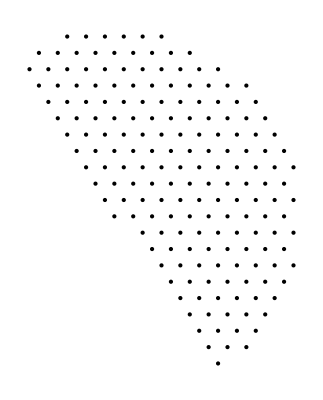

```mathematica
Graphics[Point[semiRoundParticle[10,.6,latticePoints]]]
```

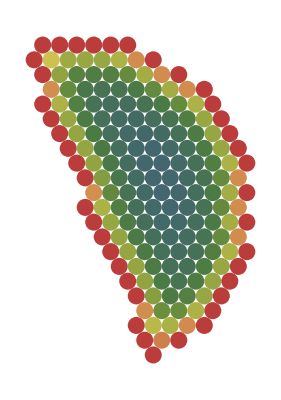

```mathematica
Graphics[particleGraphic[semiRoundParticle[10,.4,latticePoints]]]
```

```mathematica
semiRoundParticle[20,.2,latticePoints]
```

{{-3.5,18.1865},{-3.,19.0526},{-3.,17.3205},{-2.5,18.1865},{-2.,19.0526},{-1.5,19.9186},{-3.,15.5885},{-2.5,16.4545},{-2.,17.3205},{-1.5,18.1865},{-1.,19.0526},{-0.5,19.9186},{-2.5,14.7224},{-2.,15.5885},{-1.5,16.4545},{-1.,17.3205},{-0.5,18.1865},{0.,19.0526},{0.5,19.9186},{-2.5,12.9904},{-2.,13.8564},{-1.5,14.7224},{-1.,15.5885},{-0.5,16.4545},{0.,17.3205},{0.5,18.1865},{1.,19.0526},{1.5,19.9186},{-2.,12.1244},{-1.5,12.9904},{-1.,13.8564},{-0.5,14.7224},{0.,15.5885},{0.5,16.4545},{1.,17.3205},{1.5,18.1865},{2.,19.0526},{-2.,10.3923},{-1.5,11.2583},{-1.,12.1244},{-0.5,12.9904},{0.,13.8564},{0.5,14.7224},{1.,15.5885},{1.5,16.4545},{2.,17.3205},{2.5,18.1865},{3.,19.0526},{-1.5,9.52628},{-1.,10.3923},{-0.5,11.2583},{0.,12.1244},{0.5,12.9904},{1.,13.8564},{1.5,14.7224},{2.,15.5885},{2.5,16.4545},{3.,17.3205},{3.5,18.1865},{4.,19.0526},{-1.5,7.79423},{-1.,8.66025},{-0.5,9.52628},{0.,10.3923},{0.5,11.2583},{1.,12.1244},{1.5,12.9904},{2.,13.8564},{2.5,14.7224},{3.,15.5885},{3.5,16.4545},{4.,17.3205},{4.5,18.1865},{5.,19.0526},{-1.,6.9282},{-0.5,7.79423},{0.,8.66025},{0.5,9.52628},{1.,10.3923},{1.5,11.2583},{2.,12.1244},{2.5,12.9904},{3.,13.8564},{3.5,14.7224},{4.,15.5885},{4.5,16.4545},{5.,17.3205},{5.5,18.1865},{6.,19.0526},{-1.,5.19615},{-0.5,6.06218},{0.,6.9282},{0.5,7.79423},{1.,8.66025},{1.5,9.52628},{2.,10.3923},{2.5,11.2583},{3.,12.1244},{3.5,12.9904},{4.,13.8564},{4.5,14.7224},{5.,15.5885},{5.5,16.4545},{6.,17.3205},{6.5,18.1865},{-0.5,4.33013},{0.,5.19615},{0.5,6.06218},{1.,6.9282},{1.5,7.79423},{2.,8.66025},{2.5,9.52628},{3.,10.3923},{3.5,11.2583},{4.,12.1244},{4.5,12.9904},{5.,13.8564},{5.5,14.7224},{6.,15.5885},{6.5,16.4545},{7.,17.3205},{7.5,18.1865},{-0.5,2.59808},{0.,3.4641},{0.5,4.33013},{1.,5.19615},{1.5,6.06218},{2.,6.9282},{2.5,7.79423},{3.,8.66025},{3.5,9.52628},{4.,10.3923},{4.5,11.2583},{5.,12.1244},{5.5,12.9904},{6.,13.8564},{6.5,14.7224},{7.,15.5885},{7.5,16.4545},{8.,17.3205},{0.,1.73205},{0.5,2.59808},{1.,3.4641},{1.5,4.33013},{2.,5.19615},{2.5,6.06218},{3.,6.9282},{3.5,7.79423},{4.,8.66025},{4.5,9.52628},{5.,10.3923},{5.5,11.2583},{6.,12.1244},{6.5,12.9904},{7.,13.8564},{7.5,14.7224},{8.,15.5885},{8.5,16.4545},{9.,17.3205},{0.,0.},{0.5,0.866025},{1.,1.73205},{1.5,2.59808},{2.,3.4641},{2.5,4.33013},{3.,5.19615},{3.5,6.06218},{4.,6.9282},{4.5,7.79423},{5.,8.66025},{5.5,9.52628},{6.,10.3923},{6.5,11.2583},{7.,12.1244},{7.5,12.9904},{8.,13.8564},{8.5,14.7224},{9.,15.5885},{9.5,16.4545},{0.5,-0.866025},{1.,0.},{1.5,0.866025},{2.,1.73205},{2.5,2.59808},{3.,3.4641},{3.5,4.33013},{4.,5.19615},{4.5,6.06218},{5.,6.9282},{5.5,7.79423},{6.,8.66025},{6.5,9.52628},{7.,10.3923},{7.5,11.2583},{8.,12.1244},{8.5,12.9904},{9.,13.8564},{9.5,14.7224},{10.,15.5885},{10.5,16.4545},{1.,-1.73205},{1.5,-0.866025},{2.,0.},{2.5,0.866025},{3.,1.73205},{3.5,2.59808},{4.,3.4641},{4.5,4.33013},{5.,5.19615},{5.5,6.06218},{6.,6.9282},{6.5,7.79423},{7.,8.66025},{7.5,9.52628},{8.,10.3923},{8.5,11.2583},{9.,12.1244},{9.5,12.9904},{10.,13.8564},{10.5,14.7224},{11.,15.5885},{1.,-3.4641},{1.5,-2.59808},{2.,-1.73205},{2.5,-0.866025},{3.,0.},{3.5,0.866025},{4.,1.73205},{4.5,2.59808},{5.,3.4641},{5.5,4.33013},{6.,5.19615},{6.5,6.06218},{7.,6.9282},{7.5,7.79423},{8.,8.66025},{8.5,9.52628},{9.,10.3923},{9.5,11.2583},{10.,12.1244},{10.5,12.9904},{11.,13.8564},{11.5,14.7224},{12.,15.5885},{1.5,-4.33013},{2.,-3.4641},{2.5,-2.59808},{3.,-1.73205},{3.5,-0.866025},{4.,0.},{4.5,0.866025},{5.,1.73205},{5.5,2.59808},{6.,3.4641},{6.5,4.33013},{7.,5.19615},{7.5,6.06218},{8.,6.9282},{8.5,7.79423},{9.,8.66025},{9.5,9.52628},{10.,10.3923},{10.5,11.2583},{11.,12.1244},{11.5,12.9904},{12.,13.8564},{12.5,14.7224},{1.5,-6.06218},{2.,-5.19615},{2.5,-4.33013},{3.,-3.4641},{3.5,-2.59808},{4.,-1.73205},{4.5,-0.866025},{5.,0.},{5.5,0.866025},{6.,1.73205},{6.5,2.59808},{7.,3.4641},{7.5,4.33013},{8.,5.19615},{8.5,6.06218},{9.,6.9282},{9.5,7.79423},{10.,8.66025},{10.5,9.52628},{11.,10.3923},{11.5,11.2583},{12.,12.1244},{12.5,12.9904},{13.,13.8564},{13.5,14.7224},{2.,-6.9282},{2.5,-6.06218},{3.,-5.19615},{3.5,-4.33013},{4.,-3.4641},{4.5,-2.59808},{5.,-1.73205},{5.5,-0.866025},{6.,0.},{6.5,0.866025},{7.,1.73205},{7.5,2.59808},{8.,3.4641},{8.5,4.33013},{9.,5.19615},{9.5,6.06218},{10.,6.9282},{10.5,7.79423},{11.,8.66025},{11.5,9.52628},{12.,10.3923},{12.5,11.2583},{13.,12.1244},{13.5,12.9904},{14.,13.8564},{2.,-8.66025},{2.5,-7.79423},{3.,-6.9282},{3.5,-6.06218},{4.,-5.19615},{4.5,-4.33013},{5.,-3.4641},{5.5,-2.59808},{6.,-1.73205},{6.5,-0.866025},{7.,0.},{7.5,0.866025},{8.,1.73205},{8.5,2.59808},{9.,3.4641},{9.5,4.33013},{10.,5.19615},{10.5,6.06218},{11.,6.9282},{11.5,7.79423},{12.,8.66025},{12.5,9.52628},{13.,10.3923},{13.5,11.2583},{14.,12.1244},{14.5,12.9904},{2.5,-9.52628},{3.,-8.66025},{3.5,-7.79423},{4.,-6.9282},{4.5,-6.06218},{5.,-5.19615},{5.5,-4.33013},{6.,-3.4641},{6.5,-2.59808},{7.,-1.73205},{7.5,-0.866025},{8.,0.},{8.5,0.866025},{9.,1.73205},{9.5,2.59808},{10.,3.4641},{10.5,4.33013},{11.,5.19615},{11.5,6.06218},{12.,6.9282},{12.5,7.79423},{13.,8.66025},{13.5,9.52628},{14.,10.3923},{14.5,11.2583},{15.,12.1244},{2.5,-11.2583},{3.,-10.3923},{3.5,-9.52628},{4.,-8.66025},{4.5,-7.79423},{5.,-6.9282},{5.5,-6.06218},{6.,-5.19615},{6.5,-4.33013},{7.,-3.4641},{7.5,-2.59808},{8.,-1.73205},{8.5,-0.866025},{9.,0.},{9.5,0.866025},{10.,1.73205},{10.5,2.59808},{11.,3.4641},{11.5,4.33013},{12.,5.19615},{12.5,6.06218},{13.,6.9282},{13.5,7.79423},{14.,8.66025},{14.5,9.52628},{15.,10.3923},{15.5,11.2583},{3.,-12.1244},{3.5,-11.2583},{4.,-10.3923},{4.5,-9.52628},{5.,-8.66025},{5.5,-7.79423},{6.,-6.9282},{6.5,-6.06218},{7.,-5.19615},{7.5,-4.33013},{8.,-3.4641},{8.5,-2.59808},{9.,-1.73205},{9.5,-0.866025},{10.,0.},{10.5,0.866025},{11.,1.73205},{11.5,2.59808},{12.,3.4641},{12.5,4.33013},{13.,5.19615},{13.5,6.06218},{14.,6.9282},{14.5,7.79423},{15.,8.66025},{15.5,9.52628},{16.,10.3923},{16.5,11.2583},{3.,-13.8564},{3.5,-12.9904},{4.,-12.1244},{4.5,-11.2583},{5.,-10.3923},{5.5,-9.52628},{6.,-8.66025},{6.5,-7.79423},{7.,-6.9282},{7.5,-6.06218},{8.,-5.19615},{8.5,-4.33013},{9.,-3.4641},{9.5,-2.59808},{10.,-1.73205},{10.5,-0.866025},{11.,0.},{11.5,0.866025},{12.,1.73205},{12.5,2.59808},{13.,3.4641},{13.5,4.33013},{14.,5.19615},{14.5,6.06218},{15.,6.9282},{15.5,7.79423},{16.,8.66025},{16.5,9.52628},{17.,10.3923},{3.5,-14.7224},{4.,-13.8564},{4.5,-12.9904},{5.,-12.1244},{5.5,-11.2583},{6.,-10.3923},{6.5,-9.52628},{7.,-8.66025},{7.5,-7.79423},{8.,-6.9282},{8.5,-6.06218},{9.,-5.19615},{9.5,-4.33013},{10.,-3.4641},{10.5,-2.59808},{11.,-1.73205},{11.5,-0.866025},{12.,0.},{12.5,0.866025},{13.,1.73205},{13.5,2.59808},{14.,3.4641},{14.5,4.33013},{15.,5.19615},{15.5,6.06218},{16.,6.9282},{16.5,7.79423},{17.,8.66025},{17.5,9.52628},{3.5,-16.4545},{4.,-15.5885},{4.5,-14.7224},{5.,-13.8564},{5.5,-12.9904},{6.,-12.1244},{6.5,-11.2583},{7.,-10.3923},{7.5,-9.52628},{8.,-8.66025},{8.5,-7.79423},{9.,-6.9282},{9.5,-6.06218},{10.,-5.19615},{10.5,-4.33013},{11.,-3.4641},{11.5,-2.59808},{12.,-1.73205},{12.5,-0.866025},{13.,0.},{13.5,0.866025},{14.,1.73205},{14.5,2.59808},{15.,3.4641},{15.5,4.33013},{16.,5.19615},{16.5,6.06218},{17.,6.9282},{17.5,7.79423},{18.,8.66025},{4.,-17.3205},{4.5,-16.4545},{5.,-15.5885},{5.5,-14.7224},{6.,-13.8564},{6.5,-12.9904},{7.,-12.1244},{7.5,-11.2583},{8.,-10.3923},{8.5,-9.52628},{9.,-8.66025},{9.5,-7.79423},{10.,-6.9282},{10.5,-6.06218},{11.,-5.19615},{11.5,-4.33013},{12.,-3.4641},{12.5,-2.59808},{13.,-1.73205},{13.5,-0.866025},{14.,0.},{14.5,0.866025},{15.,1.73205},{15.5,2.59808},{16.,3.4641},{16.5,4.33013},{17.,5.19615},{17.5,6.06218},{18.,6.9282},{4.,-19.0526},{4.5,-18.1865},{5.,-17.3205},{5.5,-16.4545},{6.,-15.5885},{6.5,-14.7224},{7.,-13.8564},{7.5,-12.9904},{8.,-12.1244},{8.5,-11.2583},{9.,-10.3923},{9.5,-9.52628},{10.,-8.66025},{10.5,-7.79423},{11.,-6.9282},{11.5,-6.06218},{12.,-5.19615},{12.5,-4.33013},{13.,-3.4641},{13.5,-2.59808},{14.,-1.73205},{14.5,-0.866025},{15.,0.},{15.5,0.866025},{16.,1.73205},{16.5,2.59808},{17.,3.4641},{17.5,4.33013},{18.,5.19615},{18.5,6.06218},{5.,-19.0526},{5.5,-18.1865},{6.,-17.3205},{6.5,-16.4545},{7.,-15.5885},{7.5,-14.7224},{8.,-13.8564},{8.5,-12.9904},{9.,-12.1244},{9.5,-11.2583},{10.,-10.3923},{10.5,-9.52628},{11.,-8.66025},{11.5,-7.79423},{12.,-6.9282},{12.5,-6.06218},{13.,-5.19615},{13.5,-4.33013},{14.,-3.4641},{14.5,-2.59808},{15.,-1.73205},{15.5,-0.866025},{16.,0.},{16.5,0.866025},{17.,1.73205},{17.5,2.59808},{18.,3.4641},{18.5,4.33013},{19.,5.19615},{6.,-19.0526},{6.5,-18.1865},{7.,-17.3205},{7.5,-16.4545},{8.,-15.5885},{8.5,-14.7224},{9.,-13.8564},{9.5,-12.9904},{10.,-12.1244},{10.5,-11.2583},{11.,-10.3923},{11.5,-9.52628},{12.,-8.66025},{12.5,-7.79423},{13.,-6.9282},{13.5,-6.06218},{14.,-5.19615},{14.5,-4.33013},{15.,-3.4641},{15.5,-2.59808},{16.,-1.73205},{16.5,-0.866025},{17.,0.},{17.5,0.866025},{18.,1.73205},{18.5,2.59808},{19.,3.4641},{19.5,4.33013},{7.5,-18.1865},{8.,-17.3205},{8.5,-16.4545},{9.,-15.5885},{9.5,-14.7224},{10.,-13.8564},{10.5,-12.9904},{11.,-12.1244},{11.5,-11.2583},{12.,-10.3923},{12.5,-9.52628},{13.,-8.66025},{13.5,-7.79423},{14.,-6.9282},{14.5,-6.06218},{15.,-5.19615},{15.5,-4.33013},{16.,-3.4641},{16.5,-2.59808},{17.,-1.73205},{17.5,-0.866025},{18.,0.},{18.5,0.866025},{19.,1.73205},{19.5,2.59808},{9.,-17.3205},{9.5,-16.4545},{10.,-15.5885},{10.5,-14.7224},{11.,-13.8564},{11.5,-12.9904},{12.,-12.1244},{12.5,-11.2583},{13.,-10.3923},{13.5,-9.52628},{14.,-8.66025},{14.5,-7.79423},{15.,-6.9282},{15.5,-6.06218},{16.,-5.19615},{16.5,-4.33013},{17.,-3.4641},{17.5,-2.59808},{18.,-1.73205},{18.5,-0.866025},{19.,0.},{19.5,0.866025},{10.5,-16.4545},{11.,-15.5885},{11.5,-14.7224},{12.,-13.8564},{12.5,-12.9904},{13.,-12.1244},{13.5,-11.2583},{14.,-10.3923},{14.5,-9.52628},{15.,-8.66025},{15.5,-7.79423},{16.,-6.9282},{16.5,-6.06218},{17.,-5.19615},{17.5,-4.33013},{18.,-3.4641},{18.5,-2.59808},{19.,-1.73205},{19.5,-0.866025},{12.,-15.5885},{12.5,-14.7224},{13.,-13.8564},{13.5,-12.9904},{14.,-12.1244},{14.5,-11.2583},{15.,-10.3923},{15.5,-9.52628},{16.,-8.66025},{16.5,-7.79423},{17.,-6.9282},{17.5,-6.06218},{18.,-5.19615},{18.5,-4.33013},{19.,-3.4641},{19.5,-2.59808},{13.5,-14.7224},{14.,-13.8564},{14.5,-12.9904},{15.,-12.1244},{15.5,-11.2583},{16.,-10.3923},{16.5,-9.52628},{17.,-8.66025},{17.5,-7.79423},{18.,-6.9282},{18.5,-6.06218},{19.,-5.19615},{19.5,-4.33013},{16.5,-11.2583},{17.,-10.3923},{17.5,-9.52628},{18.,-8.66025}}

```mathematica
Manipulate[
Graphics[particleGraphic[semiRoundParticle[30,r,latticePoints]],PlotRange->30{{-1,1},{-1,1}}],
{r,0,2Pi},
Dynamic[totalLennardJonesTotalEnergy[semiRoundParticle[35,r,latticePoints]]]
]
```

```mathematica
orientationData =Table[
{rot,
totalLennardJonesTotalEnergy[semiRoundParticle[50,rot,latticePoints]]/(2 50)},
{rot,0,2Pi,2Pi/128}
]
```

```mathematica
refEnergy =Min[Last/@orientationData]
```

```mathematica
orientationData=orientationData/.{r_,e_}:> {r, 1 + e-refEnergy}
```

What’s up with the points along the axes?  Is the selection routine bad?

```mathematica
ListPlot[Last[#] AngleVector[First[#]]&/@orientationData, AspectRatio->1]
```

#### Computing the completely relaxed energies and minimizing positions:

```mathematica
ljEnergyFlat[positions_]:= Total[ljEnergies[Partition[positions,2]]]
```

The next calculation takes days.  A radius of 5 takes less than a minute, a radius of 10 takes about 5 hours.
15 takes about ??

```mathematica
Block[
{
positions= particles[[#]],
variables,startingPoint},
variables = Flatten[Table[{Subscript[x,i],Subscript[y,i]},{i,1,Length[positions]}]];
startingPoint = MapThread[{#1, #2}&,{variables, Flatten[positions]}];
Echo[{DateList[],#}];
{minval,minpos}=FindMinimum[ljEnergyFlat[variables],startingPoint,Method->"PrincipalAxis",MaxIterations->5000];
Echo[minval];
{minval,minpos}
]&/@{5,10,15,20}
```

#### Partial Relaxation.

The idea here is that the particles that are far from the surface will have the lattice constant that we predicted above.  Therefore the problem is broken into two parts.  Only the atoms near the surface have their full degrees of freedom.  The atoms far from the surface strain uniformly.